## See NormalOrNotv2.xlsx for a summary of the results

## The CLT

Let x_1, x_2, ..., x_n be a sequence of random variables that are identically and independenly distributed, with mean µ = 0 and variance σ^2 . Let S_n= [1/√n]   (x_1+ x_2 + ... + x_n). Then the distribution of the normalized sum S_napproaches the normal distribution N(0, σ^2) as n →∞. 

What happens when these conditions are relaxed? In the following we experiment with (a) distributions other than Normal, (b) sums of random variables that are not identically distributed, and (c) distributions with large variances (i.e. violating the Lindeberg condition).

What percentage of the values are within n standard deviations of the mean? That is the test we’ll use to determine how close a distribution comes to the normal one.

```mathematica
percentOfResults[dataSequence_, nStds_]:= Module[{nTrials, mean, std},
(* Calculate the % of results in the dataSequence that are plus or minus nStds * std of the mean. Here nStds stands for number of standard deviations (plus or minus the mean *)
nTrials = Length[dataSequence];
mean = Mean[dataSequence];
std = StandardDeviation[dataSequence];
N[Count[dataSequence,x_/; x >( mean-nStds*std) && x <(mean + nStds*std)]/nTrials]
];
```

## Experiment 1: Each random variable is normally distributed. The distributions are independent. The distributions are NOT identical. (Lyons’ baking example)

Let’s try the baking example. Baking a loaf of bread involves a number of different random variables.

Let’s begin with a different normal distribution and variance for each variable. To aid in the construction of a large number of random variables, we create a Normal distribution whose means are all different and whose standard deviations are all different but quite low compared to the means.

```mathematica
genNormalDist[mean_]:= Module[{stdFraction = (1/50.)* mean},
(* Make the standard deviation a very small fraction -- stdFraction -- of the mean *)
NormalDistribution[mean,stdFraction]
];
```

Let’s set up an nVar number of random variables each normal but with different means and standard deviations. The only constraint is that the standard deviations are small compared to the value of the means.

```mathematica
nVar = 10;
```

```mathematica
dists = Table[genNormalDist[RandomInteger[{100,700}]] ,{nVar}]
```

{NormalDistribution[469,9.38],NormalDistribution[575,11.5],NormalDistribution[459,9.18],NormalDistribution[177,3.54],NormalDistribution[561,11.22],NormalDistribution[394,7.88],NormalDistribution[308,6.16],NormalDistribution[497,9.94],NormalDistribution[270,5.4],NormalDistribution[240,4.8]}

One trial with nVar random variables looks like this.

```mathematica
vals = RandomVariate[#] & /@ dists
```

{471.705,586.34,469.834,179.641,546.802,395.717,300.441,493.257,274.619,243.445}

Adding the random variables and dividing by the square root of the number of random variables gives us:

```mathematica
tVals = (1/(nVar^0.5)) * Total[vals]
```

1252.83

Now let’s run some trials.

```mathematica
nTrials = 1000;
```

```mathematica
vals = Table[RandomVariate[#] & /@ dists, {nTrials}];
```

Add the values of the random variables for each trial.

```mathematica
tVals = (1/(nVar^0.5))*(Total[#] & /@ vals);
```

See if these values are normally distributed:

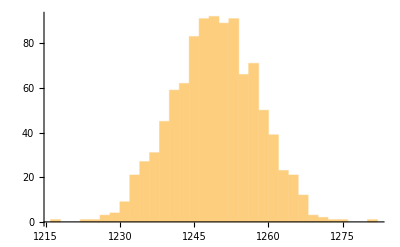

```mathematica
htVals = Histogram[tVals]
```

The percentage of results within 1, 2, and 3 standard deviations of the mean:

```mathematica
percentOfResults[tVals,#] & /@ {1,2,3}
```

{0.671,0.961,0.996}

Conclusion: Close to normal even when the CLT conditions are relaxed considerably. So the CLT can’t be the explanation for why this kind of sum of random variables sums to a normal distribution. Perhaps there are other theorems related to the CLT that have much less stringent conditions.

## Experiment 2: Each random variable is normally distributed. The distributions are NOT independent. The distributions are identical.

Let’s pick two random variables that we know are NOT independent. To satisfy the identical distributions but violate independence, let’s pick the temperature at 10 locations that are fairly close to each other.

```mathematica
wd1 = WeatherData[{45,-90}, "MaxTemperature", {{2013,01,01}, {2013, 01,10}}]
```

Missing[NotApplicable]

```mathematica
Length[wd1]
```

1

```mathematica
CityData[{"Aurora", "Illinois", "UnitedStates"}, "Coordinates"]
```

{41.7635,-88.2901}

```mathematica
cities = {"Chicago", {"Aurora", "Illinois", "UnitedStates"}, {"Skokie", "Illinois", "UnitedStates"}, {"Evanston", "Illinois", "UnitedStates"}, {"Des Plaines", "Illinois", "UnitedStates"}, {"Bolingbrook", "Illinois", "UnitedStates"}, {"Schaumburg", "Illinois", "UnitedStates"}, {"St. Charles", "Illinois", "UnitedStates"}, {"Elgin", "Illinois", "UnitedStates"}, {"Wheaton", "Illinois", "UnitedStates"}};
```

```mathematica
CityData[# , "Coordinates"] & /@ cities
```

{{41.8376,-87.6818},{41.7635,-88.2901},{42.036,-87.74},{42.0464,-87.6944},{42.0351,-87.9011},{41.6911,-88.1016},{42.0294,-88.0836},{41.9189,-88.3114},{42.0396,-88.3217},{41.8561,-88.1075}}

```mathematica
cityCoordinates = %;
```

```mathematica
cityCoordinates
```

{{41.8376,-87.6818},{41.7635,-88.2901},{42.036,-87.74},{42.0464,-87.6944},{42.0351,-87.9011},{41.6911,-88.1016},{42.0294,-88.0836},{41.9189,-88.3114},{42.0396,-88.3217},{41.8561,-88.1075}}

```mathematica
wdMaxTemp = WeatherData[#, "MaxTemperature", {{2009,01,01}, {2014, 01,01}, "Day"}] & /@ cityCoordinates;
```

```mathematica
wdMaxTempList = #[[2,1,1]] & /@ wdMaxTemp;
```

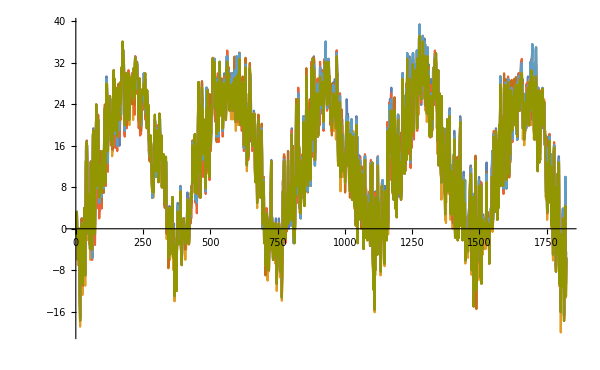

```mathematica
ListLinePlot[wdMaxTempList, ImageSize->600]
```

Remove all missing temperature values

```mathematica
wdMaxTempList[[1]][[40]] // FullForm
```

Missing["NotAvailable"]

```mathematica
wdMaxTemps = DeleteCases[#,Missing["NotAvailable"]]& /@ wdMaxTempList;
```

```mathematica
Length[#] & /@ wdMaxTemps
```

{1821,1822,1821,1821,1821,1821,1821,1822,1822,1822}

```mathematica
wdMaxTemps2 = Take[#, 1821] & /@ wdMaxTemps;
```

```mathematica
wdMaxTempsMeans = Mean[#] & /@ wdMaxTemps2
```

{14.2159,13.2586,14.2449,13.6211,14.2449,13.9514,14.2449,13.5546,13.5546,13.5567}

```mathematica
wdMaxTempsSD = StandardDeviation[#] & /@ wdMaxTemps2
```

{11.2292,11.4189,11.3018,11.1587,11.3018,11.423,11.3018,11.3682,11.3682,11.3714}

The means and standard deviations are pretty close. However, the max temperatures in the cities are *not* independent. So now let’s see if the CLT holds.

Let’s check the non-independence of the random variables. We know that if X,Y are independent then the Cov(X,Y) = 0. Let’s check the covariance between each of the vectors.

```mathematica
maxTempsCovs = Table[Covariance[wdMaxTemps2[[i]], wdMaxTemps2[[j]]], {i, 1, Length[wdMaxTemps2]}, {j, 1, Length[wdMaxTemps2]}] // TableForm
```

126.095 | 121.84 | 122.102 | 118.923 | 122.102 | 123.113 | 122.102 | 120.381 | 120.381 | 120.409
121.84 | 130.392 | 119.367 | 115.702 | 119.367 | 121.178 | 119.367 | 122.29 | 122.29 | 122.318
122.102 | 119.367 | 127.731 | 116.974 | 127.731 | 126.806 | 127.731 | 118.422 | 118.422 | 118.448
118.923 | 115.702 | 116.974 | 124.518 | 116.974 | 118.371 | 116.974 | 122.267 | 122.267 | 122.302
122.102 | 119.367 | 127.731 | 116.974 | 127.731 | 126.806 | 127.731 | 118.422 | 118.422 | 118.448
123.113 | 121.178 | 126.806 | 118.371 | 126.806 | 130.486 | 126.806 | 120.412 | 120.412 | 120.44
122.102 | 119.367 | 127.731 | 116.974 | 127.731 | 126.806 | 127.731 | 118.422 | 118.422 | 118.448
120.381 | 122.29 | 118.422 | 122.267 | 118.422 | 120.412 | 118.422 | 129.236 | 129.236 | 129.268
120.381 | 122.29 | 118.422 | 122.267 | 118.422 | 120.412 | 118.422 | 129.236 | 129.236 | 129.268
120.409 | 122.318 | 118.448 | 122.302 | 118.448 | 120.44 | 118.448 | 129.268 | 129.268 | 129.308

And we should expect the correlations to be super high as well...

```mathematica
maxTempsCorrs = Table[Correlation[wdMaxTemps2[[i]], wdMaxTemps2[[j]]], {i, 1, Length[wdMaxTemps2]}, {j, 1, Length[wdMaxTemps2]}] // TableForm
```

1. | 0.9502 | 0.962114 | 0.949078 | 0.962114 | 0.959784 | 0.962114 | 0.943012 | 0.943012 | 0.942969
0.9502 | 1. | 0.92493 | 0.908031 | 0.92493 | 0.929003 | 0.92493 | 0.942051 | 0.942051 | 0.942002
0.962114 | 0.92493 | 1. | 0.927524 | 1. | 0.982225 | 1. | 0.921709 | 0.921709 | 0.921652
0.949078 | 0.908031 | 0.927524 | 1. | 0.927524 | 0.928642 | 0.927524 | 0.963834 | 0.963834 | 0.963844
0.962114 | 0.92493 | 1. | 0.927524 | 1. | 0.982225 | 1. | 0.921709 | 0.921709 | 0.921652
0.959784 | 0.929003 | 0.982225 | 0.928642 | 0.982225 | 1. | 0.982225 | 0.92725 | 0.92725 | 0.927208
0.962114 | 0.92493 | 1. | 0.927524 | 1. | 0.982225 | 1. | 0.921709 | 0.921709 | 0.921652
0.943012 | 0.942051 | 0.921709 | 0.963834 | 0.921709 | 0.92725 | 0.921709 | 1. | 1. | 0.999967
0.943012 | 0.942051 | 0.921709 | 0.963834 | 0.921709 | 0.92725 | 0.921709 | 1. | 1. | 0.999967
0.942969 | 0.942002 | 0.921652 | 0.963844 | 0.921652 | 0.927208 | 0.921652 | 0.999967 | 0.999967 | 1.

Since the covariance is not zero we know the random variables are not independent.

```mathematica
maxTotals = Total[wdMaxTemps2];
```

```mathematica
maxTotalsNormalized = (1/(10^0.5)) * maxTotals;
```

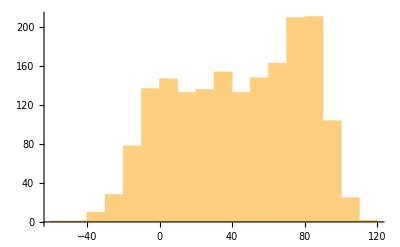

```mathematica
distMaxTotals = Histogram[maxTotalsNormalized]
```

It doesn’t look very normal. Let’s apply our normality test of checking for proportions within 1, 2, and 3 standard deviations of the mean.

```mathematica
percentOfResults[maxTotalsNormalized,#] & /@ {1,2,3}
```

{0.583745,0.987919,1.}

It’s not the right  proportion for one standard deviation from the mean but for 2 and 3 standard deviations from the mean, the distribution looks normal! Perhaps the crucial test for normality is the percentage of results that fall within 1 standard deviation of the mean.

## Experiment 3: Uniform Distributions

10 RVs each uniformly (but differently) distributed.

```mathematica
urv = Table[RandomVariate[UniformDistribution[{RandomInteger[{60,100}],RandomInteger[{400,700}]}]], {nVar}]
```

{459.008,311.945,483.666,582.696,459.563,617.283,103.009,411.986,339.074,425.336}

Sum of these 10 RVs

```mathematica
turv = Total[urv]
```

4193.57

Now sum up a series of trials of the sum of these uniformly (but differentlly) distributed RVs.

Generate the 10 distinct uniform distributions

```mathematica
udists = Table[UniformDistribution[{RandomInteger[{50,100}],RandomInteger[{400,1000}]}], {nVar}]
```

{UniformDistribution[{79,769}],UniformDistribution[{92,952}],UniformDistribution[{94,483}],UniformDistribution[{64,612}],UniformDistribution[{82,609}],UniformDistribution[{50,680}],UniformDistribution[{73,418}],UniformDistribution[{56,616}],UniformDistribution[{98,678}],UniformDistribution[{52,853}]}

```mathematica
uvals = Table[RandomVariate[#] & /@ udists, {nTrials}];
```

```mathematica
tuVals = (1/nTrials^0.5) * Total[#] & /@ uvals;
```

See if these values are normally distributed:

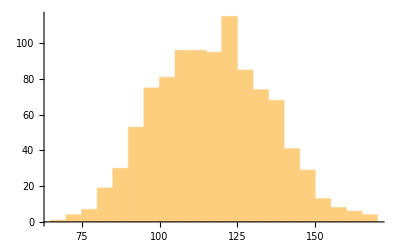

```mathematica
htuVals = Histogram[tuVals]
```

The percentage of results within 1, 2, and 3 standard deviation of the mean:

```mathematica
percentOfResults[tuVals,#] & /@ {1,2,3}
```

{0.658,0.96,1.}

Conclusion: Close to normal even when the CLT conditions are relaxed considerably.

## Experiment 4: Exponential Distributions

```mathematica
RandomVariate[ExponentialDistribution[1]] * 1000
```

631.014

10 RVs each exponentially distributed but with different lambdas.

```mathematica
edists  = Table[ExponentialDistribution[RandomReal[{0.5,2.0}]], {nVar}]
```

{ExponentialDistribution[1.65907],ExponentialDistribution[0.569643],ExponentialDistribution[1.9329],ExponentialDistribution[0.956247],ExponentialDistribution[0.815831],ExponentialDistribution[1.98072],ExponentialDistribution[1.78051],ExponentialDistribution[0.988454],ExponentialDistribution[1.80903],ExponentialDistribution[0.779364]}

Generate trials -- the 1000 multiplier here harks back to the the rough total of 1000 grams for a loaf of bread.

```mathematica
evals = Table[1000  * (RandomVariate[#] & /@ edists), {nTrials}];
```

```mathematica
teVals = (1/nTrials^0.5) * Total[#] & /@ evals;
```

See if these values are normally distributed:

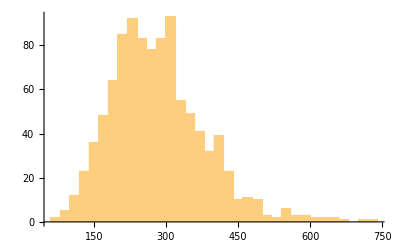

```mathematica
hteVals = Histogram[teVals]
```

The percentage of results within 1, 2, and 3 standard deviation of the mean:

```mathematica
percentOfResults[teVals,#] & /@ {0.5,1,1.5,2,3}
```

{0.403,0.711,0.898,0.961,0.988}

Conclusion: Close to normal even when the CLT conditions are relaxed considerably.

## Experiment 5: LogNormal Distributions

As we did for the Normal distributions, let’s create a generating function for the LogNormal distribution. We can control the size of the standard deviation using the stdFraction constant.

```mathematica
genLogNormalDist[mean_]:= Module[{stdFraction = (1/50.)* mean},
(* Make the standard deviation a very small fraction -- stdFraction -- of the mean *)
LogNormalDistribution[mean,stdFraction]
];
```

```mathematica
lndists = Table[genLogNormalDist[RandomInteger[{10,50}]] ,{nVar}]
```

{LogNormalDistribution[47,0.94],LogNormalDistribution[16,0.32],LogNormalDistribution[48,0.96],LogNormalDistribution[21,0.42],LogNormalDistribution[29,0.58],LogNormalDistribution[26,0.52],LogNormalDistribution[17,0.34],LogNormalDistribution[16,0.32],LogNormalDistribution[40,0.8],LogNormalDistribution[46,0.92]}

```mathematica
lnvals = RandomVariate[#] & /@ lndists
```

{1.15619×10^20,8.91866×10^6,1.4722×10^21,1.0148×10^9,2.08622×10^12,1.84545×10^11,2.00024×10^7,6.2341×10^6,2.67964×10^17,1.89681×10^20}

Adding the random variables together gives us:

```mathematica
tlnVals = Total[lnvals]
```

1.77777×10^21

```mathematica
Histogram[lnvals]
```

-Graphics-

```mathematica
RandomVariate[#] & /@ lndists
```

{3.83735×10^20,4.20573×10^6,1.80112×10^21,1.31188×10^9,2.90577×10^12,3.34049×10^11,3.44747×10^7,1.35759×10^7,3.84212×10^17,1.04812×10^20}

Now let’s run some trials.

```mathematica
lnvals = Table[RandomVariate[#] & /@ lndists, {nTrials}];
```

Add the values of the random variables for each trial.

```mathematica
tlnVals = (1/nTrials^0.5) * (Total[#] & /@ lnvals);
```

See if these values are normally distributed (skip the histogram):

The percentage of results within 1, 2, and 3 standard deviation of the mean:

```mathematica
percentOfResults[tlnVals,#] & /@ {1,2,3}
```

{0.905,0.962,0.98}

Conclusion: Quite different from normal.

## Experiment 6: Bernoulli Distribution

Generate 10 distinct Bernoulli distributions.

```mathematica
bdists = Table[BernoulliDistribution[RandomReal[]], {nVar}]
```

{BernoulliDistribution[0.810147],BernoulliDistribution[0.376194],BernoulliDistribution[0.46053],BernoulliDistribution[0.480001],BernoulliDistribution[0.841842],BernoulliDistribution[0.414367],BernoulliDistribution[0.313483],BernoulliDistribution[0.706999],BernoulliDistribution[0.192758],BernoulliDistribution[0.465739]}

```mathematica
bvals = Table[RandomVariate[#] & /@ bdists, {nTrials}];
```

```mathematica
tbVals = (1/nTrials^0.5) * Total[#] & /@ bvals;
```

See if these values are normally distributed:

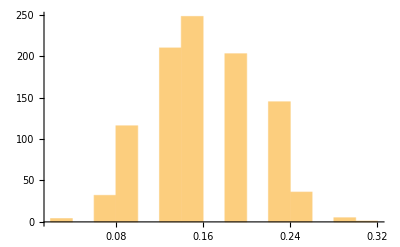

```mathematica
htbVals = Histogram[tbVals]
```

The percentage of results within 1, 2, and 3 standard deviation of the mean:

```mathematica
percentOfResults[tbVals,#] & /@ {1,2,3}
```

{0.661,0.958,0.999}

Conclusion: Close to normal even when the CLT conditions are relaxed considerably.

## Experiment 7: A Mix of Distributions

In this case we randomly pick a distribution for each RV. We pick from the sets of distributions that we’ve already created -- Normal, LogNormal, Bernoulli, Exponential, or Uniform.

Here’s the complete set of the specific distributions we’ve created so far.

```mathematica
allDists = Flatten[Fold[Append,dists, {udists, edists, lndists, bdists}]]
```

{NormalDistribution[469,9.38],NormalDistribution[575,11.5],NormalDistribution[459,9.18],NormalDistribution[177,3.54],NormalDistribution[561,11.22],NormalDistribution[394,7.88],NormalDistribution[308,6.16],NormalDistribution[497,9.94],NormalDistribution[270,5.4],NormalDistribution[240,4.8],UniformDistribution[{79,769}],UniformDistribution[{92,952}],UniformDistribution[{94,483}],UniformDistribution[{64,612}],UniformDistribution[{82,609}],UniformDistribution[{50,680}],UniformDistribution[{73,418}],UniformDistribution[{56,616}],UniformDistribution[{98,678}],UniformDistribution[{52,853}],ExponentialDistribution[1.65907],ExponentialDistribution[0.569643],ExponentialDistribution[1.9329],ExponentialDistribution[0.956247],ExponentialDistribution[0.815831],ExponentialDistribution[1.98072],ExponentialDistribution[1.78051],ExponentialDistribution[0.988454],ExponentialDistribution[1.80903],ExponentialDistribution[0.779364],LogNormalDistribution[47,0.94],LogNormalDistribution[16,0.32],LogNormalDistribution[48,0.96],LogNormalDistribution[21,0.42],LogNormalDistribution[29,0.58],LogNormalDistribution[26,0.52],LogNormalDistribution[17,0.34],LogNormalDistribution[16,0.32],LogNormalDistribution[40,0.8],LogNormalDistribution[46,0.92],BernoulliDistribution[0.810147],BernoulliDistribution[0.376194],BernoulliDistribution[0.46053],BernoulliDistribution[0.480001],BernoulliDistribution[0.841842],BernoulliDistribution[0.414367],BernoulliDistribution[0.313483],BernoulliDistribution[0.706999],BernoulliDistribution[0.192758],BernoulliDistribution[0.465739]}

Now make 10 random selections from this set to create a distinct distribution for each of the 10 RVs. Just for variety, we’ll pick 50 times just to be sure we’ve seen a wide mix of distributions.

```mathematica
mdists = Table[RandomChoice[allDists, nVar], {50}];
```

```mathematica
RandomVariate[#] & /@ mdists[[1]]
```

{6.69856×10^16,118.466,0,0,483.37,3.29716,0.282779,451.402,354.013,0}

Now let’s run some trials for each mix of distributions.

```mathematica
mvals = Table[Table[RandomVariate[#] & /@ mdists[[i]], {nTrials}], {i, 1, Length[mdists]}];
```

Add the values of the random variables for each trial.

```mathematica
tmVals = Table[(1/nTrials^0.5) * (Total[#] & /@ mvals[[i]]), {i, 1, Length[mvals]}];
```

See if these values are normally distributed (skip the histogram):

The percentage of results within 1, 2, and 3 standard deviation of the mean:

```mathematica
pr = Table[percentOfResults[tmVals[[i]],#] & /@ {1,2,3}, {i, 1, Length[tmVals]}]
```

{{0.88,0.954,0.979},{0.805,0.955,0.982},{0.92,0.969,0.984},{0.758,0.959,0.984},{0.9,0.966,0.983},{0.649,0.968,1.},{0.867,0.953,0.982},{0.741,0.958,0.984},{0.882,0.959,0.979},{0.784,0.947,0.98},{0.712,0.953,0.99},{0.902,0.961,0.982},{0.642,0.97,1.},{0.917,0.969,0.984},{0.933,0.969,0.985},{0.887,0.964,0.98},{0.648,0.964,1.},{0.92,0.968,0.982},{0.876,0.955,0.983},{0.895,0.955,0.981},{0.911,0.967,0.982},{0.646,0.972,1.},{0.736,0.954,0.99},{0.849,0.96,0.984},{0.88,0.958,0.982},{0.889,0.964,0.982},{0.66,0.967,1.},{0.714,0.961,0.989},{0.577,1.,1.},{0.699,0.95,0.997},{0.764,0.962,0.984},{0.864,0.955,0.981},{0.715,0.951,0.991},{0.914,0.957,0.976},{0.903,0.968,0.986},{0.945,0.984,0.992},{0.863,0.957,0.988},{0.736,0.956,0.986},{0.696,0.961,0.99},{0.703,0.953,0.992},{0.892,0.957,0.979},{0.889,0.957,0.985},{0.921,0.965,0.985},{0.893,0.953,0.979},{0.906,0.964,0.979},{0.757,0.95,0.988},{0.725,0.955,0.988},{0.915,0.964,0.981},{0.892,0.953,0.976},{0.891,0.964,0.983}}

Some of these percentages are about where they should be and some clearly diverge by a significant amount. Let’s see if we can detect a pattern between which mix of distributions result in a roughly normal distribution and which mix of distributions don’t.

Let’s calculate the distance between each of the above percentages and what they should be for a normal distribution. We’ll designate {0.682, 0.954, 0.998} to be the percentages for the normal distribution. Now calculate the Euclidean distance between the experimental value and the designated value for each distribution mix.

```mathematica
pnorm = {0.682, 0.954, 0.998};
```

```mathematica
ed = EuclideanDistance[pnorm, #] & /@ pr
```

{0.19891,0.12404,0.238883,0.0774403,0.218845,0.0359026,0.185693,0.0607701,0.200963,0.103812,0.0310644,0.220692,0.0431277,0.235894,0.251784,0.206032,0.0354965,0.238948,0.194582,0.21368,0.229926,0.0402989,0.0545894,0.167693,0.198686,0.207858,0.025632,0.0339706,0.114652,0.0174929,0.0835703,0.182795,0.0338674,0.23306,0.221768,0.264773,0.181301,0.0553534,0.0175784,0.0218632,0.210879,0.20743,0.239606,0.211856,0.225027,0.0757694,0.0441588,0.233833,0.211152,0.209776}

Here’s how the distances from the Normal distribution look:

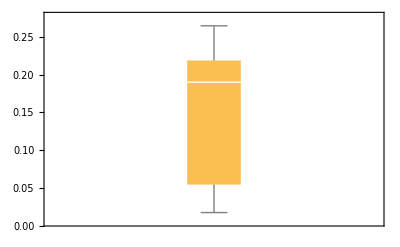

```mathematica
bp = BoxWhiskerChart[ed]
```

```mathematica
pres = Transpose[{mdists, pr, ed}];
```

```mathematica
plist = Grid[Transpose[{mdists, pr, ed}], Dividers->All];
```

Conclusion: It depends; further investigation is needed. The Excel sheet has a more readable view of the results (cf. NormalOrNot.xlsx tab “Mixes”).

## Investigate the Mixed Distributions

Look at the distribution mixes that result close-to-normal distributions -- i.e. those with Euclidean distance from Normal close to 0.

```mathematica
vLow =  Sort[Cases[pres, {x_,y_,z_} /; z ≤  0.05], #1[[3]] < #2[[3]] &];
```

```mathematica
vLowt = Sort[Cases[pres, {x_,y_,z_} /; z ≤  0.05], #1[[3]] < #2[[3]] &] // TableForm
```

BernoulliDistribution[0.192758]
BernoulliDistribution[0.192758]
ExponentialDistribution[0.956247]
NormalDistribution[575,11.5]
ExponentialDistribution[1.80903]
BernoulliDistribution[0.465739]
BernoulliDistribution[0.841842]
NormalDistribution[308,6.16]
NormalDistribution[459,9.18]
ExponentialDistribution[1.9329] | 0.699
0.95
0.997 | 0.0174929
BernoulliDistribution[0.465739]
UniformDistribution[{98,678}]
BernoulliDistribution[0.192758]
LogNormalDistribution[17,0.34]
NormalDistribution[469,9.38]
UniformDistribution[{50,680}]
BernoulliDistribution[0.465739]
LogNormalDistribution[17,0.34]
BernoulliDistribution[0.706999]
NormalDistribution[308,6.16] | 0.696
0.961
0.99 | 0.0175784
UniformDistribution[{79,769}]
UniformDistribution[{73,418}]
UniformDistribution[{64,612}]
LogNormalDistribution[16,0.32]
BernoulliDistribution[0.841842]
ExponentialDistribution[0.815831]
BernoulliDistribution[0.706999]
UniformDistribution[{82,609}]
NormalDistribution[394,7.88]
NormalDistribution[575,11.5] | 0.703
0.953
0.992 | 0.0218632
ExponentialDistribution[1.78051]
ExponentialDistribution[0.779364]
BernoulliDistribution[0.706999]
ExponentialDistribution[0.779364]
UniformDistribution[{56,616}]
NormalDistribution[561,11.22]
ExponentialDistribution[1.65907]
UniformDistribution[{64,612}]
BernoulliDistribution[0.192758]
NormalDistribution[561,11.22] | 0.66
0.967
1. | 0.025632
LogNormalDistribution[16,0.32]
UniformDistribution[{98,678}]
UniformDistribution[{79,769}]
UniformDistribution[{94,483}]
BernoulliDistribution[0.414367]
ExponentialDistribution[0.956247]
BernoulliDistribution[0.706999]
UniformDistribution[{79,769}]
ExponentialDistribution[0.815831]
NormalDistribution[469,9.38] | 0.712
0.953
0.99 | 0.0310644
BernoulliDistribution[0.841842]
ExponentialDistribution[0.988454]
NormalDistribution[177,3.54]
UniformDistribution[{73,418}]
UniformDistribution[{50,680}]
LogNormalDistribution[16,0.32]
UniformDistribution[{98,678}]
NormalDistribution[240,4.8]
LogNormalDistribution[16,0.32]
NormalDistribution[459,9.18] | 0.715
0.951
0.991 | 0.0338674
UniformDistribution[{92,952}]
BernoulliDistribution[0.465739]
LogNormalDistribution[16,0.32]
UniformDistribution[{64,612}]
UniformDistribution[{73,418}]
NormalDistribution[270,5.4]
BernoulliDistribution[0.480001]
UniformDistribution[{52,853}]
ExponentialDistribution[0.988454]
NormalDistribution[308,6.16] | 0.714
0.961
0.989 | 0.0339706
BernoulliDistribution[0.192758]
ExponentialDistribution[1.80903]
BernoulliDistribution[0.706999]
ExponentialDistribution[0.988454]
UniformDistribution[{79,769}]
ExponentialDistribution[1.65907]
BernoulliDistribution[0.414367]
ExponentialDistribution[0.569643]
UniformDistribution[{52,853}]
NormalDistribution[270,5.4] | 0.648
0.964
1. | 0.0354965
BernoulliDistribution[0.810147]
NormalDistribution[459,9.18]
ExponentialDistribution[0.815831]
UniformDistribution[{82,609}]
UniformDistribution[{52,853}]
NormalDistribution[575,11.5]
ExponentialDistribution[0.988454]
BernoulliDistribution[0.480001]
ExponentialDistribution[0.988454]
ExponentialDistribution[1.9329] | 0.649
0.968
1. | 0.0359026
NormalDistribution[469,9.38]
ExponentialDistribution[1.98072]
BernoulliDistribution[0.465739]
BernoulliDistribution[0.841842]
NormalDistribution[394,7.88]
UniformDistribution[{52,853}]
NormalDistribution[459,9.18]
UniformDistribution[{50,680}]
UniformDistribution[{73,418}]
ExponentialDistribution[1.9329] | 0.646
0.972
1. | 0.0402989
BernoulliDistribution[0.465739]
NormalDistribution[177,3.54]
NormalDistribution[308,6.16]
BernoulliDistribution[0.192758]
UniformDistribution[{79,769}]
BernoulliDistribution[0.376194]
BernoulliDistribution[0.465739]
BernoulliDistribution[0.810147]
ExponentialDistribution[1.78051]
UniformDistribution[{94,483}] | 0.642
0.97
1. | 0.0431277
ExponentialDistribution[0.988454]
UniformDistribution[{94,483}]
UniformDistribution[{98,678}]
ExponentialDistribution[0.569643]
BernoulliDistribution[0.414367]
NormalDistribution[177,3.54]
NormalDistribution[575,11.5]
UniformDistribution[{64,612}]
LogNormalDistribution[16,0.32]
NormalDistribution[497,9.94] | 0.725
0.955
0.988 | 0.0441588

```mathematica
Tally[#, Head[#1]=== Head[#2]&] & /@ vLow[[All,1]] // TableForm
```

BernoulliDistribution[0.192758]
4 | ExponentialDistribution[0.956247]
3 | NormalDistribution[575,11.5]
3 |  | 
BernoulliDistribution[0.465739]
4 | UniformDistribution[{98,678}]
2 | LogNormalDistribution[17,0.34]
2 | NormalDistribution[469,9.38]
2 | 
UniformDistribution[{79,769}]
4 | LogNormalDistribution[16,0.32]
1 | BernoulliDistribution[0.841842]
2 | ExponentialDistribution[0.815831]
1 | NormalDistribution[394,7.88]
2
ExponentialDistribution[1.78051]
4 | BernoulliDistribution[0.706999]
2 | UniformDistribution[{56,616}]
2 | NormalDistribution[561,11.22]
2 | 
LogNormalDistribution[16,0.32]
1 | UniformDistribution[{98,678}]
4 | BernoulliDistribution[0.414367]
2 | ExponentialDistribution[0.956247]
2 | NormalDistribution[469,9.38]
1
BernoulliDistribution[0.841842]
1 | ExponentialDistribution[0.988454]
1 | NormalDistribution[177,3.54]
3 | UniformDistribution[{73,418}]
3 | LogNormalDistribution[16,0.32]
2
UniformDistribution[{92,952}]
4 | BernoulliDistribution[0.465739]
2 | LogNormalDistribution[16,0.32]
1 | NormalDistribution[270,5.4]
2 | ExponentialDistribution[0.988454]
1
BernoulliDistribution[0.192758]
3 | ExponentialDistribution[1.80903]
4 | UniformDistribution[{79,769}]
2 | NormalDistribution[270,5.4]
1 | 
BernoulliDistribution[0.810147]
2 | NormalDistribution[459,9.18]
2 | ExponentialDistribution[0.815831]
4 | UniformDistribution[{82,609}]
2 | 
NormalDistribution[469,9.38]
3 | ExponentialDistribution[1.98072]
2 | BernoulliDistribution[0.465739]
2 | UniformDistribution[{52,853}]
3 | 
BernoulliDistribution[0.465739]
5 | NormalDistribution[177,3.54]
2 | UniformDistribution[{79,769}]
2 | ExponentialDistribution[1.78051]
1 | 
ExponentialDistribution[0.988454]
2 | UniformDistribution[{94,483}]
3 | BernoulliDistribution[0.414367]
1 | NormalDistribution[177,3.54]
3 | LogNormalDistribution[16,0.32]
1

```mathematica
Head[#] & /@ vLow[[1]][[1]]
```

{BernoulliDistribution,BernoulliDistribution,ExponentialDistribution,NormalDistribution,ExponentialDistribution,BernoulliDistribution,BernoulliDistribution,NormalDistribution,NormalDistribution,ExponentialDistribution}

```mathematica
# /. {a_[x1_], b_[x2_], c_[x3_], d_[x4_], e_[x5_], h_[x6_], j_[x7_], k_[x8_], r_[x9_], s_[x10_]} -> {a,b,c,d,e,h,j,k,r,s} & /@ vLow[[All,1]][[1]]
```

{BernoulliDistribution[0.192758],BernoulliDistribution[0.192758],ExponentialDistribution[0.956247],NormalDistribution[575,11.5],ExponentialDistribution[1.80903],BernoulliDistribution[0.465739],BernoulliDistribution[0.841842],NormalDistribution[308,6.16],NormalDistribution[459,9.18],ExponentialDistribution[1.9329]}

```mathematica
low = Sort[Cases[pres, {x_,y_,z_} /; z >  0.05 && z ≤ 0.1], #1[[3]] < #2[[3]] &] // TableForm
```

NormalDistribution[308,6.16]
NormalDistribution[177,3.54]
UniformDistribution[{79,769}]
UniformDistribution[{56,616}]
LogNormalDistribution[17,0.34]
BernoulliDistribution[0.841842]
BernoulliDistribution[0.465739]
UniformDistribution[{52,853}]
LogNormalDistribution[16,0.32]
NormalDistribution[308,6.16] | 0.736
0.954
0.99 | 0.0545894
UniformDistribution[{82,609}]
ExponentialDistribution[0.569643]
NormalDistribution[394,7.88]
LogNormalDistribution[17,0.34]
BernoulliDistribution[0.480001]
BernoulliDistribution[0.192758]
NormalDistribution[561,11.22]
BernoulliDistribution[0.841842]
BernoulliDistribution[0.465739]
NormalDistribution[469,9.38] | 0.736
0.956
0.986 | 0.0553534
BernoulliDistribution[0.810147]
NormalDistribution[497,9.94]
LogNormalDistribution[21,0.42]
ExponentialDistribution[0.815831]
LogNormalDistribution[16,0.32]
ExponentialDistribution[0.956247]
NormalDistribution[497,9.94]
UniformDistribution[{73,418}]
ExponentialDistribution[1.78051]
ExponentialDistribution[0.779364] | 0.741
0.958
0.984 | 0.0607701
UniformDistribution[{82,609}]
ExponentialDistribution[0.988454]
NormalDistribution[575,11.5]
ExponentialDistribution[0.988454]
UniformDistribution[{52,853}]
NormalDistribution[459,9.18]
UniformDistribution[{92,952}]
LogNormalDistribution[21,0.42]
BernoulliDistribution[0.706999]
UniformDistribution[{92,952}] | 0.757
0.95
0.988 | 0.0757694
UniformDistribution[{73,418}]
BernoulliDistribution[0.480001]
ExponentialDistribution[0.569643]
UniformDistribution[{73,418}]
BernoulliDistribution[0.465739]
UniformDistribution[{82,609}]
LogNormalDistribution[26,0.52]
NormalDistribution[459,9.18]
BernoulliDistribution[0.480001]
NormalDistribution[561,11.22] | 0.758
0.959
0.984 | 0.0774403
NormalDistribution[270,5.4]
ExponentialDistribution[1.9329]
LogNormalDistribution[29,0.58]
BernoulliDistribution[0.414367]
UniformDistribution[{64,612}]
ExponentialDistribution[0.956247]
LogNormalDistribution[16,0.32]
NormalDistribution[240,4.8]
BernoulliDistribution[0.376194]
NormalDistribution[394,7.88] | 0.764
0.962
0.984 | 0.0835703